```mathematica
Monitor[
Table[
Export["d:\\pictures\\"<>ToString[k]<>".png",
Column[
{ShowGraph5Least[k],
MatrixForm[allGraphs5[k,"matrix"]],
"signature"-> k,
"signature2"-> PadLeft[IntegerDigits[k,3],10],
"Embed"-> allGraphs5[k,"embed"],
"Relations"-> allGraphs5[k,"relations"],
"links"-> allGraphs5[k,"links"],
"parents"-> allGraphs5[k,"parents"],
"children"-> allGraphs5[k,"children"],
"comp"-> allGraphs5[k,"comp"],
"compwhy"-> allGraphs5[k,"compwhy"],
"atleast"-> allGraphs5[k,"atleast"],
"atleastwhy"-> allGraphs5[k,"atleastwhy"],
"colofour"-> allGraphs5[k,"colofour"],
"colofournull"-> allGraphs5[k,"colofournull"],
"colofourrealnull"-> allGraphs5[k,"colofourrealnull"]
},
Center
]
]
,{k,Sort[Keys[allGraphs5]]}
],k
]
```

{d:\pictures\0.png,d:\pictures\1.png,d:\pictures\2.png,d:\pictures\3.png,d:\pictures\4.png,d:\pictures\6.png,d:\pictures\9.png,d:\pictures\10.png,d:\pictures\12.png,d:\pictures\13.png,d:\pictures\14.png,d:\pictures\16.png,d:\pictures\18.png,d:\pictures\22.png,d:\pictures\26.png,d:\pictures\27.png,d:\pictures\28.png,d:\pictures\30.png,d:\pictures\31.png,d:\pictures\36.png,d:\pictures\37.png,d:\pictures\39.png,d:\pictures\40.png,d:\pictures\45.png,d:\pictures\49.png,d:\pictures\54.png,d:\pictures\63.png,d:\pictures\72.png,d:\pictures\81.png,d:\pictures\82.png,d:\pictures\84.png,d:\pictures\85.png,d:\pictures\87.png,d:\pictures\90.png,d:\pictures\91.png,d:\pictures\93.png,d:\pictures\94.png,d:\pictures\97.png,d:\pictures\108.png,d:\pictures\109.png,d:\pictures\110.png,d:\pictures\111.png,d:\pictures\112.png,d:\pictures\117.png,d:\pictures\118.png,d:\pictures\120.png,d:\pictures\121.png,d:\pictures\122.png,d:\pictures\136.png,d:\pictures\145.png,d:\pictures\162.png,d:\pictures\165.png,d:\pictures\168.png,d:\pictures\190.png,d:\pictures\193.png,d:\pictures\218.png,d:\pictures\243.png,d:\pictures\244.png,d:\pictures\245.png,d:\pictures\246.png,d:\pictures\247.png,d:\pictures\252.png,d:\pictures\253.png,d:\pictures\255.png,d:\pictures\256.png,d:\pictures\257.png,d:\pictures\270.png,d:\pictures\271.png,d:\pictures\273.png,d:\pictures\274.png,d:\pictures\276.png,d:\pictures\279.png,d:\pictures\280.png,d:\pictures\282.png,d:\pictures\283.png,d:\pictures\286.png,d:\pictures\300.png,d:\pictures\309.png,d:\pictures\324.png,d:\pictures\325.png,d:\pictures\327.png,d:\pictures\328.png,d:\pictures\333.png,d:\pictures\334.png,d:\pictures\336.png,d:\pictures\337.png,d:\pictures\342.png,d:\pictures\346.png,d:\pictures\351.png,d:\pictures\352.png,d:\pictures\353.png,d:\pictures\354.png,d:\pictures\355.png,d:\pictures\357.png,d:\pictures\360.png,d:\pictures\361.png,d:\pictures\363.png,d:\pictures\364.png,d:\pictures\365.png,d:\pictures\367.png,d:\pictures\369.png,d:\pictures\373.png,d:\pictures\377.png,d:\pictures\382.png,d:\pictures\391.png,d:\pictures\400.png,d:\pictures\414.png,d:\pictures\417.png,d:\pictures\442.png,d:\pictures\445.png,d:\pictures\448.png,d:\pictures\473.png,d:\pictures\486.png,d:\pictures\487.png,d:\pictures\488.png,d:\pictures\516.png,d:\pictures\517.png,d:\pictures\546.png,d:\pictures\576.png,d:\pictures\577.png,d:\pictures\606.png,d:\pictures\607.png,d:\pictures\608.png,d:\pictures\637.png,d:\pictures\666.png,d:\pictures\697.png,d:\pictures\728.png,d:\pictures\729.png,d:\pictures\730.png,d:\pictures\732.png,d:\pictures\733.png,d:\pictures\738.png,d:\pictures\739.png,d:\pictures\741.png,d:\pictures\742.png,d:\pictures\747.png,d:\pictures\751.png,d:\pictures\756.png,d:\pictures\757.png,d:\pictures\759.png,d:\pictures\760.png,d:\pictures\765.png,d:\pictures\766.png,d:\pictures\768.png,d:\pictures\769.png,d:\pictures\774.png,d:\pictures\778.png,d:\pictures\810.png,d:\pictures\811.png,d:\pictures\813.png,d:\pictures\814.png,d:\pictures\819.png,d:\pictures\820.png,d:\pictures\822.png,d:\pictures\823.png,d:\pictures\837.png,d:\pictures\838.png,d:\pictures\840.png,d:\pictures\841.png,d:\pictures\846.png,d:\pictures\847.png,d:\pictures\849.png,d:\pictures\850.png,d:\pictures\891.png,d:\pictures\894.png,d:\pictures\919.png,d:\pictures\922.png,d:\pictures\972.png,d:\pictures\973.png,d:\pictures\975.png,d:\pictures\976.png,d:\pictures\981.png,d:\pictures\982.png,d:\pictures\984.png,d:\pictures\985.png,d:\pictures\999.png,d:\pictures\1000.png,d:\pictures\1002.png,d:\pictures\1003.png,d:\pictures\1008.png,d:\pictures\1009.png,d:\pictures\1011.png,d:\pictures\1012.png,d:\pictures\1053.png,d:\pictures\1054.png,d:\pictures\1056.png,d:\pictures\1057.png,d:\pictures\1062.png,d:\pictures\1063.png,d:\pictures\1065.png,d:\pictures\1066.png,d:\pictures\1071.png,d:\pictures\1075.png,d:\pictures\1080.png,d:\pictures\1081.png,d:\pictures\1083.png,d:\pictures\1084.png,d:\pictures\1089.png,d:\pictures\1090.png,d:\pictures\1092.png,d:\pictures\1093.png,d:\pictures\1098.png,d:\pictures\1102.png,d:\pictures\1143.png,d:\pictures\1146.png,d:\pictures\1171.png,d:\pictures\1174.png,d:\pictures\1215.png,d:\pictures\1216.png,d:\pictures\1245.png,d:\pictures\1246.png,d:\pictures\1305.png,d:\pictures\1306.png,d:\pictures\1335.png,d:\pictures\1336.png,d:\pictures\1395.png,d:\pictures\1426.png,d:\pictures\1458.png,d:\pictures\1467.png,d:\pictures\1476.png,d:\pictures\1539.png,d:\pictures\1548.png,d:\pictures\1620.png,d:\pictures\1701.png,d:\pictures\1710.png,d:\pictures\1782.png,d:\pictures\1791.png,d:\pictures\1800.png,d:\pictures\1872.png,d:\pictures\1944.png,d:\pictures\2034.png,d:\pictures\2124.png,d:\pictures\2187.png,d:\pictures\2188.png,d:\pictures\2190.png,d:\pictures\2191.png,d:\pictures\2193.png,d:\pictures\2196.png,d:\pictures\2197.png,d:\pictures\2199.png,d:\pictures\2200.png,d:\pictures\2203.png,d:\pictures\2214.png,d:\pictures\2215.png,d:\pictures\2217.png,d:\pictures\2218.png,d:\pictures\2223.png,d:\pictures\2224.png,d:\pictures\2226.png,d:\pictures\2227.png,d:\pictures\2241.png,d:\pictures\2250.png,d:\pictures\2268.png,d:\pictures\2269.png,d:\pictures\2271.png,d:\pictures\2272.png,d:\pictures\2274.png,d:\pictures\2277.png,d:\pictures\2278.png,d:\pictures\2280.png,d:\pictures\2281.png,d:\pictures\2284.png,d:\pictures\2295.png,d:\pictures\2296.png,d:\pictures\2298.png,d:\pictures\2299.png,d:\pictures\2304.png,d:\pictures\2305.png,d:\pictures\2307.png,d:\pictures\2308.png,d:\pictures\2323.png,d:\pictures\2332.png,d:\pictures\2430.png,d:\pictures\2431.png,d:\pictures\2433.png,d:\pictures\2434.png,d:\pictures\2439.png,d:\pictures\2440.png,d:\pictures\2442.png,d:\pictures\2443.png,d:\pictures\2457.png,d:\pictures\2458.png,d:\pictures\2460.png,d:\pictures\2461.png,d:\pictures\2463.png,d:\pictures\2466.png,d:\pictures\2467.png,d:\pictures\2469.png,d:\pictures\2470.png,d:\pictures\2473.png,d:\pictures\2487.png,d:\pictures\2496.png,d:\pictures\2511.png,d:\pictures\2512.png,d:\pictures\2514.png,d:\pictures\2515.png,d:\pictures\2520.png,d:\pictures\2521.png,d:\pictures\2523.png,d:\pictures\2524.png,d:\pictures\2538.png,d:\pictures\2539.png,d:\pictures\2541.png,d:\pictures\2542.png,d:\pictures\2544.png,d:\pictures\2547.png,d:\pictures\2548.png,d:\pictures\2550.png,d:\pictures\2551.png,d:\pictures\2554.png,d:\pictures\2569.png,d:\pictures\2578.png,d:\pictures\2673.png,d:\pictures\2674.png,d:\pictures\2703.png,d:\pictures\2704.png,d:\pictures\2733.png,d:\pictures\2763.png,d:\pictures\2764.png,d:\pictures\2793.png,d:\pictures\2794.png,d:\pictures\2824.png,d:\pictures\2916.png,d:\pictures\2917.png,d:\pictures\2918.png,d:\pictures\2919.png,d:\pictures\2920.png,d:\pictures\2925.png,d:\pictures\2926.png,d:\pictures\2928.png,d:\pictures\2929.png,d:\pictures\2930.png,d:\pictures\2943.png,d:\pictures\2944.png,d:\pictures\2946.png,d:\pictures\2947.png,d:\pictures\2952.png,d:\pictures\2953.png,d:\pictures\2955.png,d:\pictures\2956.png,d:\pictures\2997.png,d:\pictures\2998.png,d:\pictures\3000.png,d:\pictures\3001.png,d:\pictures\3006.png,d:\pictures\3007.png,d:\pictures\3009.png,d:\pictures\3010.png,d:\pictures\3024.png,d:\pictures\3025.png,d:\pictures\3026.png,d:\pictures\3027.png,d:\pictures\3028.png,d:\pictures\3033.png,d:\pictures\3034.png,d:\pictures\3036.png,d:\pictures\3037.png,d:\pictures\3038.png,d:\pictures\3159.png,d:\pictures\3160.png,d:\pictures\3161.png,d:\pictures\3162.png,d:\pictures\3163.png,d:\pictures\3168.png,d:\pictures\3169.png,d:\pictures\3171.png,d:\pictures\3172.png,d:\pictures\3173.png,d:\pictures\3186.png,d:\pictures\3187.png,d:\pictures\3189.png,d:\pictures\3190.png,d:\pictures\3195.png,d:\pictures\3196.png,d:\pictures\3198.png,d:\pictures\3199.png,d:\pictures\3240.png,d:\pictures\3241.png,d:\pictures\3243.png,d:\pictures\3244.png,d:\pictures\3249.png,d:\pictures\3250.png,d:\pictures\3252.png,d:\pictures\3253.png,d:\pictures\3267.png,d:\pictures\3268.png,d:\pictures\3269.png,d:\pictures\3270.png,d:\pictures\3271.png,d:\pictures\3276.png,d:\pictures\3277.png,d:\pictures\3279.png,d:\pictures\3280.png,d:\pictures\3281.png,d:\pictures\3402.png,d:\pictures\3403.png,d:\pictures\3404.png,d:\pictures\3432.png,d:\pictures\3433.png,d:\pictures\3492.png,d:\pictures\3493.png,d:\pictures\3522.png,d:\pictures\3523.png,d:\pictures\3524.png,d:\pictures\3646.png,d:\pictures\3655.png,d:\pictures\3727.png,d:\pictures\3736.png,d:\pictures\3889.png,d:\pictures\3898.png,d:\pictures\3970.png,d:\pictures\3979.png,d:\pictures\4132.png,d:\pictures\4222.png,d:\pictures\4374.png,d:\pictures\4377.png,d:\pictures\4380.png,d:\pictures\4401.png,d:\pictures\4404.png,d:\pictures\4428.png,d:\pictures\4617.png,d:\pictures\4620.png,d:\pictures\4644.png,d:\pictures\4647.png,d:\pictures\4650.png,d:\pictures\4674.png,d:\pictures\4860.png,d:\pictures\4890.png,d:\pictures\4920.png,d:\pictures\5104.png,d:\pictures\5107.png,d:\pictures\5131.png,d:\pictures\5134.png,d:\pictures\5347.png,d:\pictures\5350.png,d:\pictures\5374.png,d:\pictures\5377.png,d:\pictures\5590.png,d:\pictures\5620.png,d:\pictures\5834.png,d:\pictures\6077.png,d:\pictures\6320.png,d:\pictures\6561.png,d:\pictures\6562.png,d:\pictures\6563.png,d:\pictures\6564.png,d:\pictures\6565.png,d:\pictures\6570.png,d:\pictures\6571.png,d:\pictures\6573.png,d:\pictures\6574.png,d:\pictures\6575.png,d:\pictures\6588.png,d:\pictures\6589.png,d:\pictures\6591.png,d:\pictures\6592.png,d:\pictures\6597.png,d:\pictures\6598.png,d:\pictures\6600.png,d:\pictures\6601.png,d:\pictures\6615.png,d:\pictures\6624.png,d:\pictures\6642.png,d:\pictures\6643.png,d:\pictures\6645.png,d:\pictures\6646.png,d:\pictures\6651.png,d:\pictures\6652.png,d:\pictures\6654.png,d:\pictures\6655.png,d:\pictures\6669.png,d:\pictures\6670.png,d:\pictures\6671.png,d:\pictures\6672.png,d:\pictures\6673.png,d:\pictures\6678.png,d:\pictures\6679.png,d:\pictures\6681.png,d:\pictures\6682.png,d:\pictures\6683.png,d:\pictures\6697.png,d:\pictures\6706.png,d:\pictures\6723.png,d:\pictures\6726.png,d:\pictures\6751.png,d:\pictures\6754.png,d:\pictures\6779.png,d:\pictures\6804.png,d:\pictures\6805.png,d:\pictures\6806.png,d:\pictures\6807.png,d:\pictures\6808.png,d:\pictures\6813.png,d:\pictures\6814.png,d:\pictures\6816.png,d:\pictures\6817.png,d:\pictures\6818.png,d:\pictures\6831.png,d:\pictures\6832.png,d:\pictures\6834.png,d:\pictures\6835.png,d:\pictures\6840.png,d:\pictures\6841.png,d:\pictures\6843.png,d:\pictures\6844.png,d:\pictures\6861.png,d:\pictures\6870.png,d:\pictures\6885.png,d:\pictures\6886.png,d:\pictures\6888.png,d:\pictures\6889.png,d:\pictures\6894.png,d:\pictures\6895.png,d:\pictures\6897.png,d:\pictures\6898.png,d:\pictures\6912.png,d:\pictures\6913.png,d:\pictures\6914.png,d:\pictures\6915.png,d:\pictures\6916.png,d:\pictures\6921.png,d:\pictures\6922.png,d:\pictures\6924.png,d:\pictures\6925.png,d:\pictures\6926.png,d:\pictures\6943.png,d:\pictures\6952.png,d:\pictures\6975.png,d:\pictures\6978.png,d:\pictures\7003.png,d:\pictures\7006.png,d:\pictures\7034.png,d:\pictures\7290.png,d:\pictures\7291.png,d:\pictures\7293.png,d:\pictures\7294.png,d:\pictures\7296.png,d:\pictures\7299.png,d:\pictures\7300.png,d:\pictures\7302.png,d:\pictures\7303.png,d:\pictures\7306.png,d:\pictures\7317.png,d:\pictures\7318.png,d:\pictures\7320.png,d:\pictures\7321.png,d:\pictures\7326.png,d:\pictures\7327.png,d:\pictures\7329.png,d:\pictures\7330.png,d:\pictures\7371.png,d:\pictures\7372.png,d:\pictures\7374.png,d:\pictures\7375.png,d:\pictures\7377.png,d:\pictures\7380.png,d:\pictures\7381.png,d:\pictures\7383.png,d:\pictures\7384.png,d:\pictures\7387.png,d:\pictures\7398.png,d:\pictures\7399.png,d:\pictures\7401.png,d:\pictures\7402.png,d:\pictures\7407.png,d:\pictures\7408.png,d:\pictures\7410.png,d:\pictures\7411.png,d:\pictures\7452.png,d:\pictures\7455.png,d:\pictures\7458.png,d:\pictures\7480.png,d:\pictures\7483.png,d:\pictures\7533.png,d:\pictures\7534.png,d:\pictures\7536.png,d:\pictures\7537.png,d:\pictures\7542.png,d:\pictures\7543.png,d:\pictures\7545.png,d:\pictures\7546.png,d:\pictures\7560.png,d:\pictures\7561.png,d:\pictures\7563.png,d:\pictures\7564.png,d:\pictures\7566.png,d:\pictures\7569.png,d:\pictures\7570.png,d:\pictures\7572.png,d:\pictures\7573.png,d:\pictures\7576.png,d:\pictures\7614.png,d:\pictures\7615.png,d:\pictures\7617.png,d:\pictures\7618.png,d:\pictures\7623.png,d:\pictures\7624.png,d:\pictures\7626.png,d:\pictures\7627.png,d:\pictures\7641.png,d:\pictures\7642.png,d:\pictures\7644.png,d:\pictures\7645.png,d:\pictures\7647.png,d:\pictures\7650.png,d:\pictures\7651.png,d:\pictures\7653.png,d:\pictures\7654.png,d:\pictures\7657.png,d:\pictures\7704.png,d:\pictures\7707.png,d:\pictures\7732.png,d:\pictures\7735.png,d:\pictures\7738.png,d:\pictures\8022.png,d:\pictures\8031.png,d:\pictures\8103.png,d:\pictures\8112.png,d:\pictures\8184.png,d:\pictures\8265.png,d:\pictures\8274.png,d:\pictures\8346.png,d:\pictures\8355.png,d:\pictures\8436.png,d:\pictures\8748.png,d:\pictures\8749.png,d:\pictures\8751.png,d:\pictures\8752.png,d:\pictures\8757.png,d:\pictures\8758.png,d:\pictures\8760.png,d:\pictures\8761.png,d:\pictures\8766.png,d:\pictures\8770.png,d:\pictures\8775.png,d:\pictures\8776.png,d:\pictures\8778.png,d:\pictures\8779.png,d:\pictures\8784.png,d:\pictures\8785.png,d:\pictures\8787.png,d:\pictures\8788.png,d:\pictures\8793.png,d:\pictures\8797.png,d:\pictures\8802.png,d:\pictures\8811.png,d:\pictures\8820.png,d:\pictures\8829.png,d:\pictures\8830.png,d:\pictures\8832.png,d:\pictures\8833.png,d:\pictures\8838.png,d:\pictures\8839.png,d:\pictures\8841.png,d:\pictures\8842.png,d:\pictures\8856.png,d:\pictures\8857.png,d:\pictures\8859.png,d:\pictures\8860.png,d:\pictures\8865.png,d:\pictures\8866.png,d:\pictures\8868.png,d:\pictures\8869.png,d:\pictures\8884.png,d:\pictures\8893.png,d:\pictures\8991.png,d:\pictures\8992.png,d:\pictures\8994.png,d:\pictures\8995.png,d:\pictures\9000.png,d:\pictures\9001.png,d:\pictures\9003.png,d:\pictures\9004.png,d:\pictures\9018.png,d:\pictures\9019.png,d:\pictures\9021.png,d:\pictures\9022.png,d:\pictures\9027.png,d:\pictures\9028.png,d:\pictures\9030.png,d:\pictures\9031.png,d:\pictures\9048.png,d:\pictures\9057.png,d:\pictures\9072.png,d:\pictures\9073.png,d:\pictures\9075.png,d:\pictures\9076.png,d:\pictures\9081.png,d:\pictures\9082.png,d:\pictures\9084.png,d:\pictures\9085.png,d:\pictures\9090.png,d:\pictures\9094.png,d:\pictures\9099.png,d:\pictures\9100.png,d:\pictures\9102.png,d:\pictures\9103.png,d:\pictures\9108.png,d:\pictures\9109.png,d:\pictures\9111.png,d:\pictures\9112.png,d:\pictures\9117.png,d:\pictures\9121.png,d:\pictures\9130.png,d:\pictures\9139.png,d:\pictures\9148.png,d:\pictures\9477.png,d:\pictures\9478.png,d:\pictures\9479.png,d:\pictures\9480.png,d:\pictures\9481.png,d:\pictures\9483.png,d:\pictures\9486.png,d:\pictures\9487.png,d:\pictures\9489.png,d:\pictures\9490.png,d:\pictures\9491.png,d:\pictures\9493.png,d:\pictures\9495.png,d:\pictures\9499.png,d:\pictures\9503.png,d:\pictures\9504.png,d:\pictures\9505.png,d:\pictures\9507.png,d:\pictures\9508.png,d:\pictures\9513.png,d:\pictures\9514.png,d:\pictures\9516.png,d:\pictures\9517.png,d:\pictures\9522.png,d:\pictures\9526.png,d:\pictures\9558.png,d:\pictures\9559.png,d:\pictures\9561.png,d:\pictures\9562.png,d:\pictures\9564.png,d:\pictures\9567.png,d:\pictures\9568.png,d:\pictures\9570.png,d:\pictures\9571.png,d:\pictures\9574.png,d:\pictures\9585.png,d:\pictures\9586.png,d:\pictures\9587.png,d:\pictures\9588.png,d:\pictures\9589.png,d:\pictures\9594.png,d:\pictures\9595.png,d:\pictures\9597.png,d:\pictures\9598.png,d:\pictures\9599.png,d:\pictures\9720.png,d:\pictures\9721.png,d:\pictures\9722.png,d:\pictures\9723.png,d:\pictures\9724.png,d:\pictures\9729.png,d:\pictures\9730.png,d:\pictures\9732.png,d:\pictures\9733.png,d:\pictures\9734.png,d:\pictures\9747.png,d:\pictures\9748.png,d:\pictures\9750.png,d:\pictures\9751.png,d:\pictures\9753.png,d:\pictures\9756.png,d:\pictures\9757.png,d:\pictures\9759.png,d:\pictures\9760.png,d:\pictures\9763.png,d:\pictures\9801.png,d:\pictures\9802.png,d:\pictures\9804.png,d:\pictures\9805.png,d:\pictures\9810.png,d:\pictures\9811.png,d:\pictures\9813.png,d:\pictures\9814.png,d:\pictures\9819.png,d:\pictures\9823.png,d:\pictures\9828.png,d:\pictures\9829.png,d:\pictures\9830.png,d:\pictures\9831.png,d:\pictures\9832.png,d:\pictures\9834.png,d:\pictures\9837.png,d:\pictures\9838.png,d:\pictures\9840.png,d:\pictures\9841.png,d:\pictures\9842.png,d:\pictures\9844.png,d:\pictures\9846.png,d:\pictures\9850.png,d:\pictures\9854.png,d:\pictures\10210.png,d:\pictures\10219.png,d:\pictures\10228.png,d:\pictures\10291.png,d:\pictures\10300.png,d:\pictures\10453.png,d:\pictures\10462.png,d:\pictures\10534.png,d:\pictures\10543.png,d:\pictures\10552.png,d:\pictures\10944.png,d:\pictures\10947.png,d:\pictures\10971.png,d:\pictures\10974.png,d:\pictures\10998.png,d:\pictures\11187.png,d:\pictures\11190.png,d:\pictures\11214.png,d:\pictures\11217.png,d:\pictures\11244.png,d:\pictures\11674.png,d:\pictures\11677.png,d:\pictures\11680.png,d:\pictures\11701.png,d:\pictures\11704.png,d:\pictures\11917.png,d:\pictures\11920.png,d:\pictures\11944.png,d:\pictures\11947.png,d:\pictures\11950.png,d:\pictures\12407.png,d:\pictures\12650.png,d:\pictures\13122.png,d:\pictures\13123.png,d:\pictures\13124.png,d:\pictures\13149.png,d:\pictures\13150.png,d:\pictures\13176.png,d:\pictures\13203.png,d:\pictures\13204.png,d:\pictures\13230.png,d:\pictures\13231.png,d:\pictures\13232.png,d:\pictures\13258.png,d:\pictures\13284.png,d:\pictures\13312.png,d:\pictures\13340.png,d:\pictures\13854.png,d:\pictures\13855.png,d:\pictures\13881.png,d:\pictures\13882.png,d:\pictures\13935.png,d:\pictures\13936.png,d:\pictures\13962.png,d:\pictures\13963.png,d:\pictures\14016.png,d:\pictures\14044.png,d:\pictures\14586.png,d:\pictures\14667.png,d:\pictures\14748.png,d:\pictures\15318.png,d:\pictures\15319.png,d:\pictures\15345.png,d:\pictures\15346.png,d:\pictures\15372.png,d:\pictures\15399.png,d:\pictures\15400.png,d:\pictures\15426.png,d:\pictures\15427.png,d:\pictures\15454.png,d:\pictures\16050.png,d:\pictures\16051.png,d:\pictures\16052.png,d:\pictures\16077.png,d:\pictures\16078.png,d:\pictures\16131.png,d:\pictures\16132.png,d:\pictures\16158.png,d:\pictures\16159.png,d:\pictures\16160.png,d:\pictures\16783.png,d:\pictures\16864.png,d:\pictures\17514.png,d:\pictures\17541.png,d:\pictures\17568.png,d:\pictures\18247.png,d:\pictures\18274.png,d:\pictures\18980.png,d:\pictures\19683.png,d:\pictures\19684.png,d:\pictures\19685.png,d:\pictures\19686.png,d:\pictures\19687.png,d:\pictures\19689.png,d:\pictures\19692.png,d:\pictures\19693.png,d:\pictures\19695.png,d:\pictures\19696.png,d:\pictures\19697.png,d:\pictures\19699.png,d:\pictures\19701.png,d:\pictures\19705.png,d:\pictures\19709.png,d:\pictures\19710.png,d:\pictures\19711.png,d:\pictures\19713.png,d:\pictures\19714.png,d:\pictures\19719.png,d:\pictures\19720.png,d:\pictures\19722.png,d:\pictures\19723.png,d:\pictures\19728.png,d:\pictures\19732.png,d:\pictures\19764.png,d:\pictures\19765.png,d:\pictures\19767.png,d:\pictures\19768.png,d:\pictures\19770.png,d:\pictures\19773.png,d:\pictures\19774.png,d:\pictures\19776.png,d:\pictures\19777.png,d:\pictures\19780.png,d:\pictures\19791.png,d:\pictures\19792.png,d:\pictures\19793.png,d:\pictures\19794.png,d:\pictures\19795.png,d:\pictures\19800.png,d:\pictures\19801.png,d:\pictures\19803.png,d:\pictures\19804.png,d:\pictures\19805.png,d:\pictures\19926.png,d:\pictures\19927.png,d:\pictures\19928.png,d:\pictures\19929.png,d:\pictures\19930.png,d:\pictures\19935.png,d:\pictures\19936.png,d:\pictures\19938.png,d:\pictures\19939.png,d:\pictures\19940.png,d:\pictures\19953.png,d:\pictures\19954.png,d:\pictures\19956.png,d:\pictures\19957.png,d:\pictures\19959.png,d:\pictures\19962.png,d:\pictures\19963.png,d:\pictures\19965.png,d:\pictures\19966.png,d:\pictures\19969.png,d:\pictures\20007.png,d:\pictures\20008.png,d:\pictures\20010.png,d:\pictures\20011.png,d:\pictures\20016.png,d:\pictures\20017.png,d:\pictures\20019.png,d:\pictures\20020.png,d:\pictures\20025.png,d:\pictures\20029.png,d:\pictures\20034.png,d:\pictures\20035.png,d:\pictures\20036.png,d:\pictures\20037.png,d:\pictures\20038.png,d:\pictures\20040.png,d:\pictures\20043.png,d:\pictures\20044.png,d:\pictures\20046.png,d:\pictures\20047.png,d:\pictures\20048.png,d:\pictures\20050.png,d:\pictures\20052.png,d:\pictures\20056.png,d:\pictures\20060.png,d:\pictures\20412.png,d:\pictures\20413.png,d:\pictures\20415.png,d:\pictures\20416.png,d:\pictures\20421.png,d:\pictures\20422.png,d:\pictures\20424.png,d:\pictures\20425.png,d:\pictures\20430.png,d:\pictures\20434.png,d:\pictures\20439.png,d:\pictures\20440.png,d:\pictures\20442.png,d:\pictures\20443.png,d:\pictures\20448.png,d:\pictures\20449.png,d:\pictures\20451.png,d:\pictures\20452.png,d:\pictures\20457.png,d:\pictures\20461.png,d:\pictures\20466.png,d:\pictures\20475.png,d:\pictures\20484.png,d:\pictures\20493.png,d:\pictures\20494.png,d:\pictures\20496.png,d:\pictures\20497.png,d:\pictures\20502.png,d:\pictures\20503.png,d:\pictures\20505.png,d:\pictures\20506.png,d:\pictures\20520.png,d:\pictures\20521.png,d:\pictures\20523.png,d:\pictures\20524.png,d:\pictures\20529.png,d:\pictures\20530.png,d:\pictures\20532.png,d:\pictures\20533.png,d:\pictures\20548.png,d:\pictures\20557.png,d:\pictures\20655.png,d:\pictures\20656.png,d:\pictures\20658.png,d:\pictures\20659.png,d:\pictures\20664.png,d:\pictures\20665.png,d:\pictures\20667.png,d:\pictures\20668.png,d:\pictures\20682.png,d:\pictures\20683.png,d:\pictures\20685.png,d:\pictures\20686.png,d:\pictures\20691.png,d:\pictures\20692.png,d:\pictures\20694.png,d:\pictures\20695.png,d:\pictures\20712.png,d:\pictures\20721.png,d:\pictures\20736.png,d:\pictures\20737.png,d:\pictures\20739.png,d:\pictures\20740.png,d:\pictures\20745.png,d:\pictures\20746.png,d:\pictures\20748.png,d:\pictures\20749.png,d:\pictures\20754.png,d:\pictures\20758.png,d:\pictures\20763.png,d:\pictures\20764.png,d:\pictures\20766.png,d:\pictures\20767.png,d:\pictures\20772.png,d:\pictures\20773.png,d:\pictures\20775.png,d:\pictures\20776.png,d:\pictures\20781.png,d:\pictures\20785.png,d:\pictures\20794.png,d:\pictures\20803.png,d:\pictures\20812.png,d:\pictures\21168.png,d:\pictures\21177.png,d:\pictures\21186.png,d:\pictures\21249.png,d:\pictures\21258.png,d:\pictures\21411.png,d:\pictures\21420.png,d:\pictures\21492.png,d:\pictures\21501.png,d:\pictures\21510.png,d:\pictures\21870.png,d:\pictures\21871.png,d:\pictures\21873.png,d:\pictures\21874.png,d:\pictures\21876.png,d:\pictures\21879.png,d:\pictures\21880.png,d:\pictures\21882.png,d:\pictures\21883.png,d:\pictures\21886.png,d:\pictures\21897.png,d:\pictures\21898.png,d:\pictures\21900.png,d:\pictures\21901.png,d:\pictures\21906.png,d:\pictures\21907.png,d:\pictures\21909.png,d:\pictures\21910.png,d:\pictures\21951.png,d:\pictures\21952.png,d:\pictures\21954.png,d:\pictures\21955.png,d:\pictures\21957.png,d:\pictures\21960.png,d:\pictures\21961.png,d:\pictures\21963.png,d:\pictures\21964.png,d:\pictures\21967.png,d:\pictures\21978.png,d:\pictures\21979.png,d:\pictures\21981.png,d:\pictures\21982.png,d:\pictures\21987.png,d:\pictures\21988.png,d:\pictures\21990.png,d:\pictures\21991.png,d:\pictures\22032.png,d:\pictures\22035.png,d:\pictures\22038.png,d:\pictures\22060.png,d:\pictures\22063.png,d:\pictures\22113.png,d:\pictures\22114.png,d:\pictures\22116.png,d:\pictures\22117.png,d:\pictures\22122.png,d:\pictures\22123.png,d:\pictures\22125.png,d:\pictures\22126.png,d:\pictures\22140.png,d:\pictures\22141.png,d:\pictures\22143.png,d:\pictures\22144.png,d:\pictures\22146.png,d:\pictures\22149.png,d:\pictures\22150.png,d:\pictures\22152.png,d:\pictures\22153.png,d:\pictures\22156.png,d:\pictures\22194.png,d:\pictures\22195.png,d:\pictures\22197.png,d:\pictures\22198.png,d:\pictures\22203.png,d:\pictures\22204.png,d:\pictures\22206.png,d:\pictures\22207.png,d:\pictures\22221.png,d:\pictures\22222.png,d:\pictures\22224.png,d:\pictures\22225.png,d:\pictures\22227.png,d:\pictures\22230.png,d:\pictures\22231.png,d:\pictures\22233.png,d:\pictures\22234.png,d:\pictures\22237.png,d:\pictures\22284.png,d:\pictures\22287.png,d:\pictures\22312.png,d:\pictures\22315.png,d:\pictures\22318.png,d:\pictures\22599.png,d:\pictures\22600.png,d:\pictures\22601.png,d:\pictures\22602.png,d:\pictures\22603.png,d:\pictures\22608.png,d:\pictures\22609.png,d:\pictures\22611.png,d:\pictures\22612.png,d:\pictures\22613.png,d:\pictures\22626.png,d:\pictures\22627.png,d:\pictures\22629.png,d:\pictures\22630.png,d:\pictures\22635.png,d:\pictures\22636.png,d:\pictures\22638.png,d:\pictures\22639.png,d:\pictures\22653.png,d:\pictures\22662.png,d:\pictures\22680.png,d:\pictures\22681.png,d:\pictures\22683.png,d:\pictures\22684.png,d:\pictures\22689.png,d:\pictures\22690.png,d:\pictures\22692.png,d:\pictures\22693.png,d:\pictures\22707.png,d:\pictures\22708.png,d:\pictures\22709.png,d:\pictures\22710.png,d:\pictures\22711.png,d:\pictures\22716.png,d:\pictures\22717.png,d:\pictures\22719.png,d:\pictures\22720.png,d:\pictures\22721.png,d:\pictures\22735.png,d:\pictures\22744.png,d:\pictures\22761.png,d:\pictures\22764.png,d:\pictures\22789.png,d:\pictures\22792.png,d:\pictures\22817.png,d:\pictures\22842.png,d:\pictures\22843.png,d:\pictures\22844.png,d:\pictures\22845.png,d:\pictures\22846.png,d:\pictures\22851.png,d:\pictures\22852.png,d:\pictures\22854.png,d:\pictures\22855.png,d:\pictures\22856.png,d:\pictures\22869.png,d:\pictures\22870.png,d:\pictures\22872.png,d:\pictures\22873.png,d:\pictures\22878.png,d:\pictures\22879.png,d:\pictures\22881.png,d:\pictures\22882.png,d:\pictures\22899.png,d:\pictures\22908.png,d:\pictures\22923.png,d:\pictures\22924.png,d:\pictures\22926.png,d:\pictures\22927.png,d:\pictures\22932.png,d:\pictures\22933.png,d:\pictures\22935.png,d:\pictures\22936.png,d:\pictures\22950.png,d:\pictures\22951.png,d:\pictures\22952.png,d:\pictures\22953.png,d:\pictures\22954.png,d:\pictures\22959.png,d:\pictures\22960.png,d:\pictures\22962.png,d:\pictures\22963.png,d:\pictures\22964.png,d:\pictures\22981.png,d:\pictures\22990.png,d:\pictures\23013.png,d:\pictures\23016.png,d:\pictures\23041.png,d:\pictures\23044.png,d:\pictures\23072.png,d:\pictures\23356.png,d:\pictures\23365.png,d:\pictures\23437.png,d:\pictures\23446.png,d:\pictures\23518.png,d:\pictures\23599.png,d:\pictures\23608.png,d:\pictures\23680.png,d:\pictures\23689.png,d:\pictures\23770.png,d:\pictures\24138.png,d:\pictures\24141.png,d:\pictures\24144.png,d:\pictures\24165.png,d:\pictures\24168.png,d:\pictures\24381.png,d:\pictures\24384.png,d:\pictures\24408.png,d:\pictures\24411.png,d:\pictures\24414.png,d:\pictures\24868.png,d:\pictures\24871.png,d:\pictures\24895.png,d:\pictures\24898.png,d:\pictures\24922.png,d:\pictures\25111.png,d:\pictures\25114.png,d:\pictures\25138.png,d:\pictures\25141.png,d:\pictures\25168.png,d:\pictures\25625.png,d:\pictures\25868.png,d:\pictures\26244.png,d:\pictures\26245.png,d:\pictures\26246.png,d:\pictures\26247.png,d:\pictures\26248.png,d:\pictures\26253.png,d:\pictures\26254.png,d:\pictures\26256.png,d:\pictures\26257.png,d:\pictures\26258.png,d:\pictures\26271.png,d:\pictures\26272.png,d:\pictures\26274.png,d:\pictures\26275.png,d:\pictures\26280.png,d:\pictures\26281.png,d:\pictures\26283.png,d:\pictures\26284.png,d:\pictures\26325.png,d:\pictures\26326.png,d:\pictures\26328.png,d:\pictures\26329.png,d:\pictures\26334.png,d:\pictures\26335.png,d:\pictures\26337.png,d:\pictures\26338.png,d:\pictures\26352.png,d:\pictures\26353.png,d:\pictures\26354.png,d:\pictures\26355.png,d:\pictures\26356.png,d:\pictures\26361.png,d:\pictures\26362.png,d:\pictures\26364.png,d:\pictures\26365.png,d:\pictures\26366.png,d:\pictures\26487.png,d:\pictures\26488.png,d:\pictures\26489.png,d:\pictures\26490.png,d:\pictures\26491.png,d:\pictures\26496.png,d:\pictures\26497.png,d:\pictures\26499.png,d:\pictures\26500.png,d:\pictures\26501.png,d:\pictures\26514.png,d:\pictures\26515.png,d:\pictures\26517.png,d:\pictures\26518.png,d:\pictures\26523.png,d:\pictures\26524.png,d:\pictures\26526.png,d:\pictures\26527.png,d:\pictures\26568.png,d:\pictures\26569.png,d:\pictures\26571.png,d:\pictures\26572.png,d:\pictures\26577.png,d:\pictures\26578.png,d:\pictures\26580.png,d:\pictures\26581.png,d:\pictures\26595.png,d:\pictures\26596.png,d:\pictures\26597.png,d:\pictures\26598.png,d:\pictures\26599.png,d:\pictures\26604.png,d:\pictures\26605.png,d:\pictures\26607.png,d:\pictures\26608.png,d:\pictures\26609.png,d:\pictures\26730.png,d:\pictures\26731.png,d:\pictures\26732.png,d:\pictures\26760.png,d:\pictures\26761.png,d:\pictures\26820.png,d:\pictures\26821.png,d:\pictures\26850.png,d:\pictures\26851.png,d:\pictures\26852.png,d:\pictures\26973.png,d:\pictures\26974.png,d:\pictures\26976.png,d:\pictures\26977.png,d:\pictures\26979.png,d:\pictures\26982.png,d:\pictures\26983.png,d:\pictures\26985.png,d:\pictures\26986.png,d:\pictures\26989.png,d:\pictures\27000.png,d:\pictures\27001.png,d:\pictures\27003.png,d:\pictures\27004.png,d:\pictures\27009.png,d:\pictures\27010.png,d:\pictures\27012.png,d:\pictures\27013.png,d:\pictures\27027.png,d:\pictures\27036.png,d:\pictures\27054.png,d:\pictures\27055.png,d:\pictures\27057.png,d:\pictures\27058.png,d:\pictures\27060.png,d:\pictures\27063.png,d:\pictures\27064.png,d:\pictures\27066.png,d:\pictures\27067.png,d:\pictures\27070.png,d:\pictures\27081.png,d:\pictures\27082.png,d:\pictures\27084.png,d:\pictures\27085.png,d:\pictures\27090.png,d:\pictures\27091.png,d:\pictures\27093.png,d:\pictures\27094.png,d:\pictures\27109.png,d:\pictures\27118.png,d:\pictures\27216.png,d:\pictures\27217.png,d:\pictures\27219.png,d:\pictures\27220.png,d:\pictures\27225.png,d:\pictures\27226.png,d:\pictures\27228.png,d:\pictures\27229.png,d:\pictures\27243.png,d:\pictures\27244.png,d:\pictures\27246.png,d:\pictures\27247.png,d:\pictures\27249.png,d:\pictures\27252.png,d:\pictures\27253.png,d:\pictures\27255.png,d:\pictures\27256.png,d:\pictures\27259.png,d:\pictures\27273.png,d:\pictures\27282.png,d:\pictures\27297.png,d:\pictures\27298.png,d:\pictures\27300.png,d:\pictures\27301.png,d:\pictures\27306.png,d:\pictures\27307.png,d:\pictures\27309.png,d:\pictures\27310.png,d:\pictures\27324.png,d:\pictures\27325.png,d:\pictures\27327.png,d:\pictures\27328.png,d:\pictures\27330.png,d:\pictures\27333.png,d:\pictures\27334.png,d:\pictures\27336.png,d:\pictures\27337.png,d:\pictures\27340.png,d:\pictures\27355.png,d:\pictures\27364.png,d:\pictures\27459.png,d:\pictures\27460.png,d:\pictures\27489.png,d:\pictures\27490.png,d:\pictures\27519.png,d:\pictures\27549.png,d:\pictures\27550.png,d:\pictures\27579.png,d:\pictures\27580.png,d:\pictures\27610.png,d:\pictures\27732.png,d:\pictures\27741.png,d:\pictures\27813.png,d:\pictures\27822.png,d:\pictures\27975.png,d:\pictures\27984.png,d:\pictures\28056.png,d:\pictures\28065.png,d:\pictures\28218.png,d:\pictures\28308.png,d:\pictures\28431.png,d:\pictures\28432.png,d:\pictures\28434.png,d:\pictures\28435.png,d:\pictures\28440.png,d:\pictures\28441.png,d:\pictures\28443.png,d:\pictures\28444.png,d:\pictures\28449.png,d:\pictures\28453.png,d:\pictures\28458.png,d:\pictures\28459.png,d:\pictures\28461.png,d:\pictures\28462.png,d:\pictures\28467.png,d:\pictures\28468.png,d:\pictures\28470.png,d:\pictures\28471.png,d:\pictures\28476.png,d:\pictures\28480.png,d:\pictures\28512.png,d:\pictures\28513.png,d:\pictures\28515.png,d:\pictures\28516.png,d:\pictures\28521.png,d:\pictures\28522.png,d:\pictures\28524.png,d:\pictures\28525.png,d:\pictures\28539.png,d:\pictures\28540.png,d:\pictures\28542.png,d:\pictures\28543.png,d:\pictures\28548.png,d:\pictures\28549.png,d:\pictures\28551.png,d:\pictures\28552.png,d:\pictures\28593.png,d:\pictures\28596.png,d:\pictures\28621.png,d:\pictures\28624.png,d:\pictures\28674.png,d:\pictures\28675.png,d:\pictures\28677.png,d:\pictures\28678.png,d:\pictures\28683.png,d:\pictures\28684.png,d:\pictures\28686.png,d:\pictures\28687.png,d:\pictures\28701.png,d:\pictures\28702.png,d:\pictures\28704.png,d:\pictures\28705.png,d:\pictures\28710.png,d:\pictures\28711.png,d:\pictures\28713.png,d:\pictures\28714.png,d:\pictures\28755.png,d:\pictures\28756.png,d:\pictures\28758.png,d:\pictures\28759.png,d:\pictures\28764.png,d:\pictures\28765.png,d:\pictures\28767.png,d:\pictures\28768.png,d:\pictures\28773.png,d:\pictures\28777.png,d:\pictures\28782.png,d:\pictures\28783.png,d:\pictures\28785.png,d:\pictures\28786.png,d:\pictures\28791.png,d:\pictures\28792.png,d:\pictures\28794.png,d:\pictures\28795.png,d:\pictures\28800.png,d:\pictures\28804.png,d:\pictures\28845.png,d:\pictures\28848.png,d:\pictures\28873.png,d:\pictures\28876.png,d:\pictures\28917.png,d:\pictures\28918.png,d:\pictures\28947.png,d:\pictures\28948.png,d:\pictures\29007.png,d:\pictures\29008.png,d:\pictures\29037.png,d:\pictures\29038.png,d:\pictures\29097.png,d:\pictures\29128.png,d:\pictures\29160.png,d:\pictures\29161.png,d:\pictures\29162.png,d:\pictures\29163.png,d:\pictures\29164.png,d:\pictures\29166.png,d:\pictures\29169.png,d:\pictures\29170.png,d:\pictures\29172.png,d:\pictures\29173.png,d:\pictures\29174.png,d:\pictures\29176.png,d:\pictures\29178.png,d:\pictures\29182.png,d:\pictures\29186.png,d:\pictures\29187.png,d:\pictures\29188.png,d:\pictures\29190.png,d:\pictures\29191.png,d:\pictures\29196.png,d:\pictures\29197.png,d:\pictures\29199.png,d:\pictures\29200.png,d:\pictures\29205.png,d:\pictures\29209.png,d:\pictures\29214.png,d:\pictures\29223.png,d:\pictures\29232.png,d:\pictures\29241.png,d:\pictures\29242.png,d:\pictures\29244.png,d:\pictures\29245.png,d:\pictures\29247.png,d:\pictures\29250.png,d:\pictures\29251.png,d:\pictures\29253.png,d:\pictures\29254.png,d:\pictures\29257.png,d:\pictures\29268.png,d:\pictures\29269.png,d:\pictures\29270.png,d:\pictures\29271.png,d:\pictures\29272.png,d:\pictures\29277.png,d:\pictures\29278.png,d:\pictures\29280.png,d:\pictures\29281.png,d:\pictures\29282.png,d:\pictures\29296.png,d:\pictures\29305.png,d:\pictures\29322.png,d:\pictures\29325.png,d:\pictures\29328.png,d:\pictures\29350.png,d:\pictures\29353.png,d:\pictures\29378.png,d:\pictures\29403.png,d:\pictures\29404.png,d:\pictures\29405.png,d:\pictures\29406.png,d:\pictures\29407.png,d:\pictures\29412.png,d:\pictures\29413.png,d:\pictures\29415.png,d:\pictures\29416.png,d:\pictures\29417.png,d:\pictures\29430.png,d:\pictures\29431.png,d:\pictures\29433.png,d:\pictures\29434.png,d:\pictures\29436.png,d:\pictures\29439.png,d:\pictures\29440.png,d:\pictures\29442.png,d:\pictures\29443.png,d:\pictures\29446.png,d:\pictures\29460.png,d:\pictures\29469.png,d:\pictures\29484.png,d:\pictures\29485.png,d:\pictures\29487.png,d:\pictures\29488.png,d:\pictures\29493.png,d:\pictures\29494.png,d:\pictures\29496.png,d:\pictures\29497.png,d:\pictures\29502.png,d:\pictures\29506.png,d:\pictures\29511.png,d:\pictures\29512.png,d:\pictures\29513.png,d:\pictures\29514.png,d:\pictures\29515.png,d:\pictures\29517.png,d:\pictures\29520.png,d:\pictures\29521.png,d:\pictures\29523.png,d:\pictures\29524.png,d:\pictures\29525.png,d:\pictures\29527.png,d:\pictures\29529.png,d:\pictures\29533.png,d:\pictures\29537.png,d:\pictures\29542.png,d:\pictures\29551.png,d:\pictures\29560.png,d:\pictures\29574.png,d:\pictures\29577.png,d:\pictures\29602.png,d:\pictures\29605.png,d:\pictures\29608.png,d:\pictures\29633.png,d:\pictures\29646.png,d:\pictures\29647.png,d:\pictures\29648.png,d:\pictures\29676.png,d:\pictures\29677.png,d:\pictures\29706.png,d:\pictures\29736.png,d:\pictures\29737.png,d:\pictures\29766.png,d:\pictures\29767.png,d:\pictures\29768.png,d:\pictures\29797.png,d:\pictures\29826.png,d:\pictures\29857.png,d:\pictures\29888.png,d:\pictures\29920.png,d:\pictures\29929.png,d:\pictures\29938.png,d:\pictures\30001.png,d:\pictures\30010.png,d:\pictures\30082.png,d:\pictures\30163.png,d:\pictures\30172.png,d:\pictures\30244.png,d:\pictures\30253.png,d:\pictures\30262.png,d:\pictures\30334.png,d:\pictures\30406.png,d:\pictures\30496.png,d:\pictures\30586.png,d:\pictures\30708.png,d:\pictures\30711.png,d:\pictures\30735.png,d:\pictures\30738.png,d:\pictures\30951.png,d:\pictures\30954.png,d:\pictures\30978.png,d:\pictures\30981.png,d:\pictures\31194.png,d:\pictures\31224.png,d:\pictures\31438.png,d:\pictures\31441.png,d:\pictures\31444.png,d:\pictures\31465.png,d:\pictures\31468.png,d:\pictures\31492.png,d:\pictures\31681.png,d:\pictures\31684.png,d:\pictures\31708.png,d:\pictures\31711.png,d:\pictures\31714.png,d:\pictures\31738.png,d:\pictures\31924.png,d:\pictures\31954.png,d:\pictures\31984.png,d:\pictures\32198.png,d:\pictures\32441.png,d:\pictures\32684.png,d:\pictures\33048.png,d:\pictures\33049.png,d:\pictures\33050.png,d:\pictures\33075.png,d:\pictures\33076.png,d:\pictures\33129.png,d:\pictures\33130.png,d:\pictures\33156.png,d:\pictures\33157.png,d:\pictures\33158.png,d:\pictures\33780.png,d:\pictures\33781.png,d:\pictures\33807.png,d:\pictures\33808.png,d:\pictures\33834.png,d:\pictures\33861.png,d:\pictures\33862.png,d:\pictures\33888.png,d:\pictures\33889.png,d:\pictures\33916.png,d:\pictures\34539.png,d:\pictures\34620.png,d:\pictures\35244.png,d:\pictures\35245.png,d:\pictures\35271.png,d:\pictures\35272.png,d:\pictures\35325.png,d:\pictures\35326.png,d:\pictures\35352.png,d:\pictures\35353.png,d:\pictures\35406.png,d:\pictures\35434.png,d:\pictures\35976.png,d:\pictures\35977.png,d:\pictures\35978.png,d:\pictures\36003.png,d:\pictures\36004.png,d:\pictures\36030.png,d:\pictures\36057.png,d:\pictures\36058.png,d:\pictures\36084.png,d:\pictures\36085.png,d:\pictures\36086.png,d:\pictures\36112.png,d:\pictures\36138.png,d:\pictures\36166.png,d:\pictures\36194.png,d:\pictures\36736.png,d:\pictures\36817.png,d:\pictures\36898.png,d:\pictures\37521.png,d:\pictures\37548.png,d:\pictures\38254.png,d:\pictures\38281.png,d:\pictures\38308.png,d:\pictures\39014.png,d:\pictures\39366.png,d:\pictures\39367.png,d:\pictures\39368.png,d:\pictures\39369.png,d:\pictures\39370.png,d:\pictures\39372.png,d:\pictures\39375.png,d:\pictures\39376.png,d:\pictures\39378.png,d:\pictures\39379.png,d:\pictures\39380.png,d:\pictures\39382.png,d:\pictures\39384.png,d:\pictures\39388.png,d:\pictures\39392.png,d:\pictures\40122.png,d:\pictures\40123.png,d:\pictures\40125.png,d:\pictures\40126.png,d:\pictures\40131.png,d:\pictures\40132.png,d:\pictures\40134.png,d:\pictures\40135.png,d:\pictures\40140.png,d:\pictures\40144.png,d:\pictures\40878.png,d:\pictures\40887.png,d:\pictures\40896.png,d:\pictures\41634.png,d:\pictures\41635.png,d:\pictures\41637.png,d:\pictures\41638.png,d:\pictures\41640.png,d:\pictures\41643.png,d:\pictures\41644.png,d:\pictures\41646.png,d:\pictures\41647.png,d:\pictures\41650.png,d:\pictures\42390.png,d:\pictures\42391.png,d:\pictures\42392.png,d:\pictures\42393.png,d:\pictures\42394.png,d:\pictures\42399.png,d:\pictures\42400.png,d:\pictures\42402.png,d:\pictures\42403.png,d:\pictures\42404.png,d:\pictures\43147.png,d:\pictures\43156.png,d:\pictures\43902.png,d:\pictures\43905.png,d:\pictures\43908.png,d:\pictures\44659.png,d:\pictures\44662.png,d:\pictures\45416.png,d:\pictures\46170.png,d:\pictures\46171.png,d:\pictures\46172.png,d:\pictures\46173.png,d:\pictures\46174.png,d:\pictures\46179.png,d:\pictures\46180.png,d:\pictures\46182.png,d:\pictures\46183.png,d:\pictures\46184.png,d:\pictures\46926.png,d:\pictures\46927.png,d:\pictures\46929.png,d:\pictures\46930.png,d:\pictures\46932.png,d:\pictures\46935.png,d:\pictures\46936.png,d:\pictures\46938.png,d:\pictures\46939.png,d:\pictures\46942.png,d:\pictures\47685.png,d:\pictures\47694.png,d:\pictures\48438.png,d:\pictures\48439.png,d:\pictures\48441.png,d:\pictures\48442.png,d:\pictures\48447.png,d:\pictures\48448.png,d:\pictures\48450.png,d:\pictures\48451.png,d:\pictures\48456.png,d:\pictures\48460.png,d:\pictures\49194.png,d:\pictures\49195.png,d:\pictures\49196.png,d:\pictures\49197.png,d:\pictures\49198.png,d:\pictures\49200.png,d:\pictures\49203.png,d:\pictures\49204.png,d:\pictures\49206.png,d:\pictures\49207.png,d:\pictures\49208.png,d:\pictures\49210.png,d:\pictures\49212.png,d:\pictures\49216.png,d:\pictures\49220.png,d:\pictures\49954.png,d:\pictures\49963.png,d:\pictures\49972.png,d:\pictures\50715.png,d:\pictures\50718.png,d:\pictures\51472.png,d:\pictures\51475.png,d:\pictures\51478.png,d:\pictures\52232.png,d:\pictures\52974.png,d:\pictures\52975.png,d:\pictures\52976.png,d:\pictures\53733.png,d:\pictures\53734.png,d:\pictures\54492.png,d:\pictures\55251.png,d:\pictures\55252.png,d:\pictures\56010.png,d:\pictures\56011.png,d:\pictures\56012.png,d:\pictures\56770.png,d:\pictures\57528.png,d:\pictures\58288.png,d:\pictures\59048.png}

```mathematica
Keys[allGraphs5[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofournull,colofourrealnull,atleast,embed,atleastwhy}

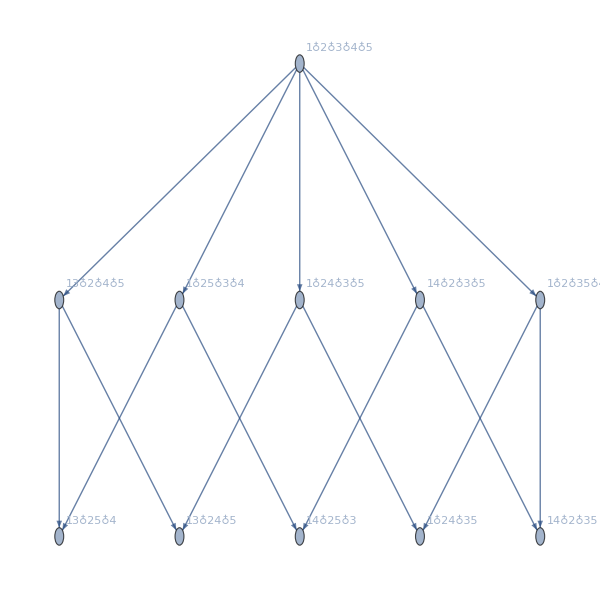
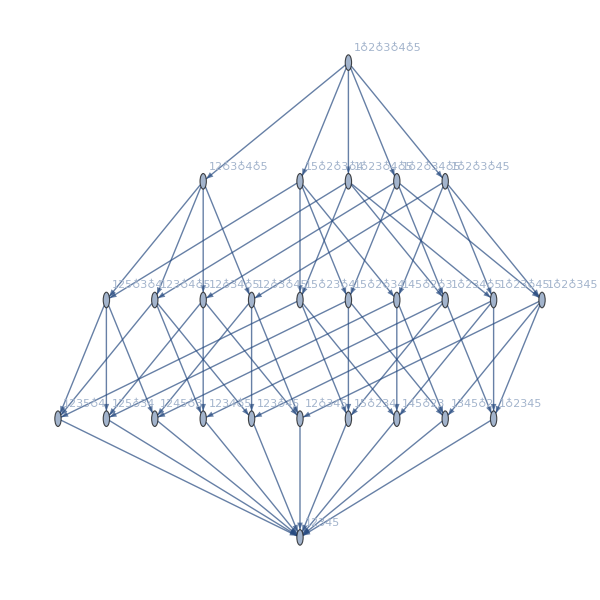
{-Graphics-206655
(2 | 1 | 0 | 0 | 1
1 | 2 | 1 | 0 | 0
0 | 1 | 2 | 1 | 0
0 | 0 | 1 | 2 | 1
1 | 0 | 0 | 1 | 2)
signature→20665
signature2→{1,0,0,1,1,0,0,1,0,1}
Embed→63
Relations→{x20665==x27226+x35977,x20665==x22852+x31681,x20665==x20746+x23041,x20665==x20692+x20803,x20665==x20668+x27259,x20665==x20664-x22856,x20665==x20656-x20758,x20665==x20422-x27550,x20665==x19936-x23608,x20665==-x46936+x982}
links→{}
parents→{20664,20656,20422,19936,982}
children→{{27226,35977},{22852,31681},{20746,23041},{20692,20803},{20668,27259}}
comp→Greater
compwhy→This is a planar contraction
atleast→5
atleastwhy→Propagate from relation {27226, 35977} with values {4, 1}
colofour→v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5
colofournull→1/6 (p12345+2 p123x45-p124x35+2 p125x34+2 p12x345+p12x34x5-2 p12x35x4+p12x3x45-p134x25-p135x24-p13x245+p13x24x5+p13x25x4-2 p13x2x45+2 p145x23-p14x235-2 p14x23x5+p14x25x3+p14x2x35+2 p15x234+p15x23x4-2 p15x24x3+p15x2x34+p1x23x45+p1x24x35-2 p1x25x34)
colofourrealnull→4 n12345-n1234x5-n1235x4-n123x45+n123x4x5-n1245x3-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1345x2-n145x23+n145x2x3-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5
colofour→-Graphics-

colofourrealnull→-Graphics-}

```mathematica
Table[
Column[
{Show[ShowGraph5Least[k],ImageSize->600],
MatrixForm[allGraphs5[k,"matrix"]],
"signature"-> k,
"signature2"-> PadLeft[IntegerDigits[k,3],10],
"Embed"-> allGraphs5[k,"embed"],
"Relations"-> allGraphs5[k,"relations"],
"links"-> allGraphs5[k,"links"],
"parents"-> allGraphs5[k,"parents"],
"children"-> allGraphs5[k,"children"],
"comp"-> allGraphs5[k,"comp"],
"compwhy"-> allGraphs5[k,"compwhy"],
"atleast"-> allGraphs5[k,"atleast"],
"atleastwhy"-> allGraphs5[k,"atleastwhy"],
"colofour"-> allGraphs5[k,"colofour"],
"colofournull"-> allGraphs5[k,"colofournull"],
"colofourrealnull"-> allGraphs5[k,"colofourrealnull"],
"colofour"->Graph[FormulaGraph[ allGraphs5[k,"colofour"]],ImageSize->{600,600}],,
"colofourrealnull"->Graph[FormulaGraph[ allGraphs5[k,"colofourrealnull"]],ImageSize->{600,600}]
},
Center
]
,{k,{lambdaKey}}
]
```